```mathematica
ClearAll["Global`*"]
```

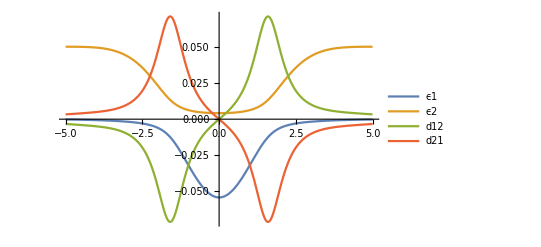

```mathematica
(* define electronic Hamiltonian *)
A0 = 0.10;
B0 =0.28;
C0 = 0.015;
D0 = 0.06;
E0 =0.05;
H = ({{0, C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), -A0 ⅇ^(-B0 x^2)+E0}});

(* solve electronic Hamiltonian *)
{{ϵ1,ϵ2},{v1,v2}}=Eigensystem[H];
v1/=Sqrt[v1.v1];
v2/=Sqrt[v2.v2];

(* find nonadiabatic coupling of adiabatic states *)
d12 = v1.D[v2, x];
d21 = v2.D[v1, x];

(* check surfaces *)
Plot[{ϵ1,ϵ2,d12/12.,d21/12.},{x,-5,5},PlotLegends->{"ϵ1","ϵ2","d12","d21"}]
```

```mathematica
kmax=10;
```

```mathematica
ntraj=5;
```

```mathematica
surfaceprobTrace=Range[kmax+1];
```

```mathematica
kTrace=Range[kmax];
```

```mathematica
kcount=0;
posmax=7.0;
```

```mathematica
(*outer loop over k*)
For[k=0,k≤kmax,k++,
(* simulation parameters *)
kcount+=1;
m=1;
x0=-4.0;
v0=k/m/20;
dt=0.1;
c1=0.6;
c2=√(1.-Abs[c1]^2);
ℏ=1;
nstep = 500;

(*surface = ϵ1;
force = -∂_x surface;
onSurface1 = True;
numHops = 0;

pos = x0;
vel = v0;
posTrace = Range[nstep];
velTrace = Range[nstep];
potTrace = Range[nstep];
surfaceTrace = Range[nstep];
energyTrace = Range[nstep];
c1Trace = Range[nstep];
c2Trace = Range[nstep];
prob1to2Trace=Range[nstep];
prob2to1Trace=Range[nstep];
surfcount=0;*)

surfcount=0;

(*outer loop over trajectories*)
For[traj=1,traj≤ntraj,traj++,

surface = ϵ1;
force = -D[surface, x];
onSurface1 = True;
numHops = 0;

pos = x0;
vel = v0;
posTrace = Range[nstep]; posTrace[[All]]=0;
velTrace = Range[nstep];velTrace[[All]]=0;
potTrace = Range[nstep];potTrace[[All]]=0;
surfaceTrace = Range[nstep];surfaceTrace[[All]]=0;
energyTrace = Range[nstep];energyTrace[[All]]=0;
c1Trace = Range[nstep];c1Trace[[All]]=0;
c2Trace = Range[nstep];c2Trace[[All]]=0;
prob1to2Trace=Range[nstep];prob1to2Trace[[All]]=0;
prob2to1Trace=Range[nstep];prob2to1Trace[[All]]=0;


(*inner loop over time steps--> propagate trajectory*)
For[t=1,t≤nstep,t++,
(* record observables *)
posTrace[[t]]=pos;
velTrace[[t]]=vel;
energy = 0.5*m*vel^2+(surface/.{x->pos});
energyTrace[[t]] = energy;
potTrace[[t]]=(surface/.{x->pos});
surfaceTrace[[t]] = Boole[onSurface1];
c1Trace[[t]]=c1;
c2Trace[[t]]=c2;

(* propagate the electronic state forward *)
d21 = -(d12/.x->pos);
c1 += dt*((c1*(ϵ1/.x->pos))/(ⅈ ℏ)-c2*vel*(d12/.x->pos));
c2 += dt*((c2*(ϵ2/.x->pos))/(ⅈ ℏ)+c1*vel*(d12/.x->pos));

(* decide hopping  *)
a11=c1*c1;
a22=c2*c2;
a12=c1*c2;
a21=c2*c1;
b12=-2*Re[a12*vel*(d12/.x->pos)];
b21=-2*Re[a21*vel*d21];

hopped=False;
prob1to2Trace[[t]] = Abs[dt*b21/a11];
prob2to1Trace[[t]] = Abs[dt*b12/a22];
If[!hopped && Abs[dt*b21/a11]>RandomReal[]&& onSurface1,
(* hop from 1 to 2 *)
(*kinetic = energy-(ϵ2/.{x->pos});
If[kinetic>0,surface = ϵ2;hopped=True;]*)
hopped=True;
surface=ϵ2;
];
If[!hopped && Abs[dt*b12/a22]>RandomReal[]&& !onSurface1,
(* hop from 2 to 1 *)
(*kinetic = energy-(ϵ1/.{x->pos});
If[kinetic>0,surface = ϵ1;hopped=True;]*)
hopped=True;
surface=ϵ1;
(*Tcup Added*)
onSurface1=True;
];
If[hopped,
onSurface1=!onSurface1;
numHops+=1;
force = -D[surface, x]; (* recalculate force *)

(*vel = Sign[vel]*√((2*kinetic)/m);*)
];

(* propagate the heavy particle forward *)
a0 = force/m/.x->pos;
pos += vel*dt+0.5*a0*dt^2;
a1 = force/m/.x->pos;
vel += 0.5*(a0+a1)*dt;

(* Test to see if on surface1 or not *)
If[onSurface1&&((t==nstep)||pos ≥ posmax),surfcount+=1];
If[pos≥posmax,Break[]]

]
(*If[onSurface1&&(t==nstep),surfcount+=1]*)
(*If[onSurface1&&((t==nstep)||pos ≥ posmax),surfcount+=1];*)
(*If[pos≥posmax,Break[]]*)
];
surfaceprobTrace[[kcount]]=surfcount/ntraj;
]
numHops
```

2

```mathematica
kcount
```

11

```mathematica
surfcount
```

0

```mathematica
surfaceprobTrace
```

{3/5,0,0,1/5,0,0,0,0,0,1/5,0}

```mathematica
onSurface1
```

False

```mathematica
pos
```

7.02276

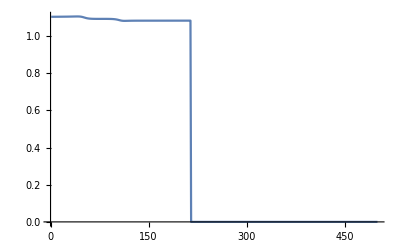

```mathematica
ListLinePlot[{Abs[c2Trace]^2+Abs[c1Trace]^2}]
```

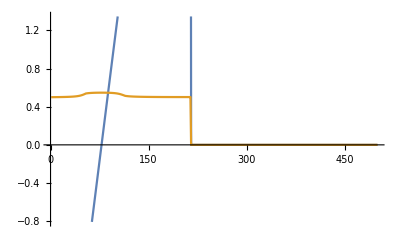

```mathematica
ListLinePlot[{posTrace,velTrace}]
```

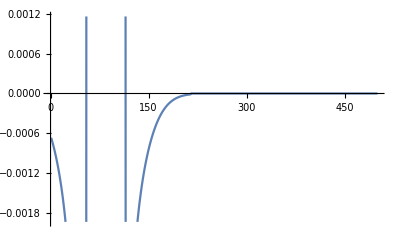

```mathematica
ListLinePlot[potTrace]
```

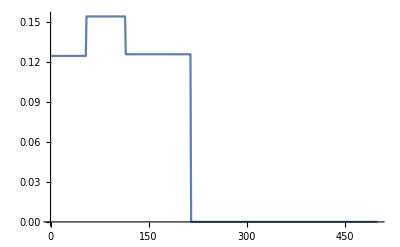

```mathematica
ListLinePlot[energyTrace]
```

```mathematica
Show[{
ListPlot[{posTrace,potTrace}//Transpose,PlotMarkers->"x"],
Plot[{ϵ1,ϵ2},{x,-5,5},PlotLegends->{"ϵ1","ϵ2","d12"},PlotStyle->Thick]
}]
```

-Graphics-